```mathematica
sol1=DSolve[{D[r^2 f[r],r]==λ r^2 f[r]},f[r],r]
```

{{f[r]→(ⅇ^(r λ) C[1])/r^2}}

```mathematica
D[r^2 f[r],r]/r^2==λf[r]
```

(2 r f[r]+r^2 f'[r])/r^2==λf[r]

```mathematica
Exp[(i+1) l h]/((i+1)h)-Exp[(i-1)l h]/((i-1)h)//FullSimplify
```

(2 ⅇ^(h i l) (-Cosh[h l]+i Sinh[h l]))/(h (-1+i^2))

```mathematica
(2 ⅇ^(h i l) (-Cosh[h l]+i Sinh[h l]))/(h (-1+i^2))/.Exp[h i l]-> y i^2 h^2
```

(2 h i^2 y (-Cosh[h l]+i Sinh[h l]))/(-1+i^2)

```mathematica
Reduce[2/z+(-Cosh[z]+Sinh[z])/z≤1,z,Complexes]
```

$Aborted

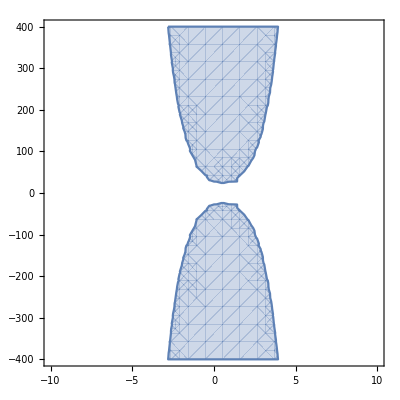

```mathematica
q=2;
RegionPlot[Abs[(2 i)/(a+b I)+i^4((-Cosh[a+b I]+i Sinh[a+b I])/(a+b I))]≤1/.i->q,{a,-10,10},{b,-100 i^i,100 i^i}/.i->q]
```